# データ処理のための数学

## データと処理系

### データとは

処理系が扱える表現全てがデータである。

演算装置（CPU/GPU/NPU）内の処理では「instruction」と「data」に明確に分かれる。

#### データ型

ほとんどすべての処理系やプログラミング言語ではデータ型が定義されている。

基本的な型：

- 整数(Integer)

- 浮動小数(Real)

- ブール代数

- 文字

- アドレス/ポインタ

上位構造（基本の組み合わせ）：

- 配列

-- ベクトル

-- 行列

-- テンソル

-- 文字列

- 複素数(Complex)

- 構造体

- 列挙型

- リスト(連結セル)

#### 指定子

データ型をさらに修飾する宣言：

- long

- double

- singed

- unsigined

### 処理系とは

OSおよびその上で動作するアプリケーション。

### 計算機（資源）

処理系を動作させるための物理的環境。

演算装置（CPU/GPU/NPU）

メインメモリー

外部記憶装置

入力装置

出力装置

外部通信装置

以上を接続・制御する制御装置

## データ構造とデータ種別

### データ構造

- 計算機から見ればデータ型の組み合わせ。

- 利用者から見ればいわゆるデータフォーマット。

### データ種別

定性値

名義尺度
値は、命名、分類のために用いられる。
数え上げ
集合/順序組 ?

順序尺度
値は、序列、順序を示す。
数えること + 序列に関する統計的扱い
位相 ?

定量値

間隔尺度
間隔に意味があるが、原点がない。
数えること + 序列に関する統計的扱い + 足し算引き算
加算に対して閉じている系
ほぼ（?）群

比率尺度
原点からの距離を表す。
数えること + 序列に関する統計的扱い + 足し算引き算 + 掛け算割り算
ほぼ（?）体

## 数と群・環・体

### 群・環・体

https://note.com/suupen/n/n171b2839cf3b

### 群・環・体と数値データの関係

群・環・体における数は無限精度の無限集合である一方、計算機で利用する数値データは有限精度・有限集合である。

計算機で利用するデータには数値以外に文字・ポインタ・構造体の概念がある。

符号なし整数 ->自然数の一部

符号付整数 -> 整数の一部

浮動小数 -> 実数/有理数の一部

## 類似度と距離

### 類似度の概念

ふたつの個体が似ていることを定義する(この関数をSとする)。

三つの個体(Va、Vb、Vc)を考える。

VaとVbがVaとVcより似ているなら:
S(Va,Vb) > S(Va,Vc).00.00䀐

反射律: S(Va,Va) = 1 ; 完全に一致すれば1

対称律: S(Va,Vb) = S(Vb,Va) ; どちらから見ても類似度は同じ

### 非類似度の概念

ふたつの個体が似ていないことを定義する(この関数をDSとする)。

VaとVbがVaとVcより似ているなら:
S(Va,Vb) < S(Va,Vc).00.00䀐

反射律: DS(Va,Va) = 0 ; 完全に一致すれば0

対称律: DS(Va,Vb) = DS(Vb,Va) ; どちらから見ても非類似度は同じ

### 距離の概念

ふたつの個体のあいだの空間(距離)を定義する(この関数をDとする)。

VaとVbがVaとVcより近いなら:
D(Va,Vb) < D(Va,Vc).00.00䀐

反射律: D(Va,Va) = 0 ; 完全に一致すれば0

対称律: D(Va,Vb) = D(Vb,Va) ; どちらから見ても距離は同じ

推移律: D(Va,Vc) <= D(Va,Vb) + D(Vb,Vc); VaとVcの距離は、VaとVbの距離とVbとVcの距離の合計以下となる

### 個体間の距離・類似度

1変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

多変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

### 名義尺度をもとにした類似度

{0,1}型データ、つまり、各カテゴリに対して1(属する)、0(属さない)の形。

m: 両方とも1

n: 両方とも0

o: {0,1}

p: {1,0}

t: アイテム数(要素数)

```mathematica
va={0,0,1,1,0}
vb={1,1,0,1,0}
```

{0,0,1,1,0}

{1,1,0,1,0}

一致係数: S(Va,Vb) = (m+n)/t

```mathematica
s[1][va_,vb_]:=Count[Map[Apply[Equal,#]&,Transpose[{va,vb}]],True]/Length[va]
```

```mathematica
s[1][va,vb]
```

2/5

類似比:

```mathematica
s[2][va_,vb_]:=Module[{trl,m,n,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
t=Length[trl];
m/(t-n)
]
```

```mathematica
s[2][va,vb]
```

1/4

Rogers-Tanimotoの係数:

```mathematica
s[3][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(m+n)/(t+o+p)
]
```

```mathematica
s[3][va,vb]
```

1/4

Hamannの係数:

```mathematica
s[4][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
((m+n)-(o+p))/t
]
```

```mathematica
s[4][va,vb]
```

-1/5

Russel-Raoの係数:

```mathematica
s[5][va_,vb_]:=Module[{trl,m,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
t=Length[trl];
m/t
]
```

```mathematica
s[5][va,vb]
```

1/5

ファイ係数: S(Va,Vb) = (mn - op) / ((m+o) (p+n) (m+p) (o+n))^(1/2)

```mathematica
s[6][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(m n - o p) / ((m+o) (p+n) (m+p) (o+n))^(1/2)
]
```

```mathematica
s[6][va,vb]
```

-1/6

### 名義尺度をもとにした距離

{0,1}型データ、つまり、各カテゴリに対して1(属する)、0(属さない)の形。

不一致係数: D(Va,Vb) = (o+p)/t

```mathematica
d[1][va_,vb_]:=Module[{trl,o,p,t},
trl=Transpose[{va,vb}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(o+p)/t
]
```

```mathematica
d[1][va,vb]
```

3/5

ハミング距離: D(Va,Vb) = o+p

```mathematica
d[2][va_,vb_]:=Module[{trl,o,p},
trl=Transpose[{va,vb}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
(o+p)
]
```

```mathematica
d[2][va,vb]
```

3

```mathematica
??HammingDistance
```

```mathematica
HammingDistance[va,vb]
```

3

### 順序尺度をもとにした類似度

スピアマンの順位相関

```mathematica
??SpearmanRho
```

ケンドールの順位相関

```mathematica
??KendallTau
```

### 定量値(間隔尺度、比率尺度)をもとにした類似度

各要素は変数値

```mathematica
va={2,3,1,3,4}
vb={2,1,1,4,4}
vc=va
```

{2,3,1,3,4}

{2,1,1,4,4}

{2,3,1,3,4}

パターン類似度: S(Va,Vb) = ∑v_ai v_bi / (∑v_ai^2 v_bi^2)^(1/2)

```mathematica
s[7][va_,vb_]:=Tr[va*vb]/Sqrt[Tr[va^2]*Tr[vb^2]]
```

```mathematica
s[7][va,vb]
```

6 √(6/247)

```mathematica
s[7][va,vc]
```

1

相関係数: S(Va,Vb) = sab / (saa sbb)^(1/2) ; saa = ∑(v_ai- mean(v_a))^2 / t ; sab = ∑(v_ai - mean(v_a))(v_bi - mean(v_b)) / t

```mathematica
??Correlation
```

コサイン類似度: S(Va,Vb) = cos(Va,Vb)

```mathematica
1-CosineDistance[va,vb]
```

6 √(6/247)

内積(反射率は満たさない): S(Va,Vb) = ∑_(i=1)^(|Va|) a[i]*b[i]

```mathematica
??Inner
```

### 定量値(間隔尺度、比率尺度)をもとにした距離

ユークリッド距離: D(Va,Vb) = (∑(v_ai-v_bi)^2)^(1/2)

```mathematica
??EuclideanDistance
```

重み付きユークリッド距離: D(Va,Vb) = (∑(ki(v_ai-v_bi))^2)^(1/2) ; k_i = 重み

標準化ユークリッド距離: D(Va,Vb) = (∑1/si(v_ai-v_bi)^2)^(1/2) ; si = ∑_(j=1)^N (v_ji-mean(v_i)) / N ; N =  個体数(a,bのふたつ)

市街距離(マンハッタン距離): D(Va,Vb) = ∑|v_ai-v_bi|

```mathematica
??ManhattanDistance
```

ミンコフスキー距離: D(Va,Vb,k) = (∑|v_ai-v_bi|^k)^(1/k) ; k = 1のときマンハッタン距離、k = 2のときユークリッド距離

マハラノビスの汎距離: D(Va,Vb) = (∑∑(v_ai - v_bj)w_ij(v_aj - v_bi))^(1/2) ; w_ij = 1/(u-1)∑_(r=1)^u [(v_ri-mean(v_i))(v_rj-mean(v_j))] 、分散共分散行列の逆行列

マハラノビスの汎距離: D(Va,Vb) = Sqrt[(v_a-v_b)^Tσ^-1(v_a - v_b)] ; T:転置; σ^-1: 分散共分散行列の逆行列、サンプルの大きさ (平均と分散)を考慮(標準化)した距離。

コサイン距離 : D (Va, Vb) = 1 - cos (Va, Vb)

```mathematica
??CosineDistance
```

### 文字列間の距離・類似度

#### 編集距離

編集距離(レーベンシュタイン距離): 二つの文の間で、片方の文をどのように編集すれば、もう片方の文になるかのステップをカウント。

置換に関しては、1とカウントする場合と2(削除・挿入)とカウントする場合がある。

```mathematica
??EditDistance
```

```mathematica
EditDistance["C","A"]
```

1

```mathematica
EditDistance["C",""]
```

1

```mathematica
EditDistance["","A"]
```

1

```mathematica
EditDistance["ABC","ACB"]
```

2

```mathematica
EditDistance["ABCD","ADCA"]
```

2

```mathematica
EditDistance["ABCD","ADC"]
```

2

#### サブ文字列出現頻度ベクトルによる距離

- N-gramやタームのカウントによるベクトル間の距離(黒板)

### 個体群間の距離・類似度

個体群の代表値（平均値/中央値/最大値/最小値）を用いる

## 数値データ分布とモデル

### 分布モデル

#### 準備(統計の復習)

統計の基本的定理: 大数の法則、中心極限定理をもとに考えられたモデル

n次モーメント: Integrate[x^n f[x], {-Inf, +Inf}, dx]は、f[x]が原点におよぼすn次モーメントである。

(モーメント)平滑指数(天野による定義、n次モーメントの値をより低い次数のモーメントの値で割ったもの): Integrate[x^n f[x],dx] / Integrate[x^m f[x],dx] ; n>m(通常、n=m+1)

確率密度分布の0次モーメントは1である。

度数分布の0次モーメント(表現がヘンだが)はサンプル総数である。

したがって、平均値は一種の平滑値でありその値は “1次モーメントの値/0次モーメントの値” となる。
(のちに、正規分布を例に詳しく見る)

#### 確率密度関数 (PDF: Probability Density Function)

PDFの-無限大から+無限大までの積分が1。

すべての区間で負の値をとらない。

```mathematica
??PDF
```

```mathematica
PDF[NormalDistribution[0, 1], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}]
```

1

#### 累積分布関数 (CDF: Cumulative Distribution Function)

cdf(x) =∫_(-∞)^x pdf(t)ⅆt

PDFの-無限大からxまでの積分。x -> 無限大で、1に収束。

```mathematica
??CDF
```

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

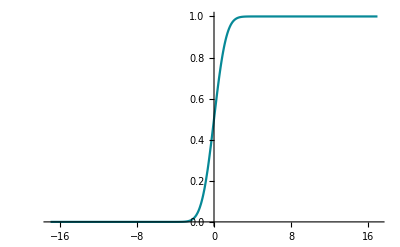

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

#### 二重指数関数

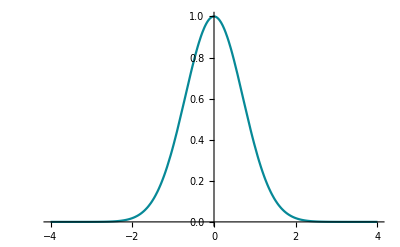

```mathematica
Plot[E^-(x^2),{x,-4,4}]
```

```mathematica
Integrate[E^-(x^2),{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[E^-(-m+x)^2,{x,-Infinity,Infinity}]
```

√π

#### 正規分布#

正規分布の式、m:平均、s:標準偏差

```mathematica
PDF[NormalDistribution[m,s], x]
```

(ⅇ^(-(-m+x)^2/(2 s^2)))/(√(2 π) s)

正規分布の形

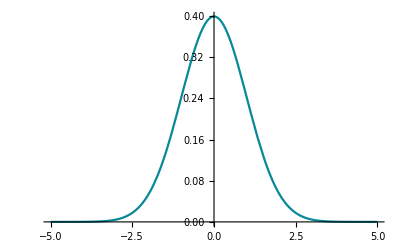

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}] (*0次モーメント*)
```

1

```mathematica
Integrate[(x^0) PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}] (*0次モーメント:明示的表現*)
```

1

1次モーメント / 0次モーメントは平均と一致する

```mathematica
Integrate[x PDF[NormalDistribution[m,1],x],{x,-Infinity,Infinity}](*1次モーメント*)
```

m

```mathematica
Integrate[(x^1) PDF[NormalDistribution[m,4],x],{x,-Infinity,Infinity}](*1次モーメント:明示的表現*)
```

m

度数分布の場合も同じ

```mathematica
l2={1,2,1,2,3,4,5,1,3,6}
```

{1,2,1,2,3,4,5,1,3,6}

```mathematica
Tally[l2]
```

{{1,3},{2,2},{3,2},{4,1},{5,1},{6,1}}

度数の合計 = 関数における0次モーメント

```mathematica
Map[#[[2]]&,Tally[l2]]//Tr
```

10

数値の合計 = 度数*数値要素の合計 = 関数における1次モーメント

```mathematica
Map[#[[1]]*#[[2]]&,Tally[l2]]//Tr
```

28

1次モーメント/0次モーメント = 平均

```mathematica
28/10
```

14/5

```mathematica
Mean[l2]
```

14/5

2次モーメントは分散と一致する(平均がゼロの場合)

```mathematica
Integrate[x^2 PDF[NormalDistribution[0,3],x],{x,-Infinity,Infinity}]
```

9

(x - mean(x))に対する2次モーメントは分散と一致する

```mathematica
Integrate[(x-4)^2 PDF[NormalDistribution[4,3],x],{x,-Infinity,Infinity}]
```

9

関数 CentralMoment[] は平均に対するn次モーメントを与える

```mathematica
CentralMoment[NormalDistribution[0,3],2]
```

9

```mathematica
CentralMoment[NormalDistribution[4,3],2]
```

9

正規分布の歪度(3次モーメント/2次モーメント^(3/2))は0

```mathematica
Skewness[NormalDistribution[0,1]]
```

0

正規分布の尖度(4次モーメント/2次モーメント^2)は3

```mathematica
Kurtosis[NormalDistribution[0,1]]
```

3

正規分布の変曲点は平均値±標準偏差の値と一致する

```mathematica
Solve[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{x→m-s},{x→m+s}}

```mathematica
Reduce[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

s≠0&&(x==m+s||x==m-s)

```mathematica
FourierTransform[PDF[NormalDistribution[0,t]],t,w]
```

FourierTransform[Function[x,(ⅇ^(-x^2/(2 t^2)))/(√(2 π) t)],t,w]

正規分布のフーリエ変換は正規分布となる

```mathematica
PDF[NormalDistribution[0,1]][t]
```

(ⅇ^(-t^2/2))/(√(2 π))

```mathematica
FourierTransform[PDF[NormalDistribution[0,1]][t],t,w]
```

(ⅇ^(-w^2/2))/(√(2 π))

```mathematica
PDF[NormalDistribution[0,1]][w]===FourierTransform[PDF[NormalDistribution[0,1]][t],t,w]
```

True

#### その他の分布 : 二項分布

```mathematica
PDF[BinomialDistribution[n, p], k]
```

Piecewise[{{(1-p)^(-k+n) p^k Binomial[n,k], 0≤k≤n}, {0, True}}]

```mathematica
n!/(k! (n - k)!) (* = Binomial[n,k] *)
```

(n!)/(k! (-k+n)!)

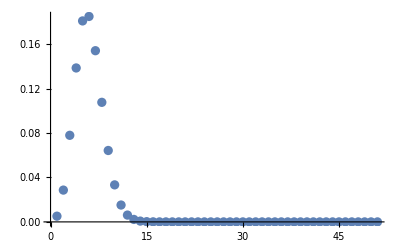

```mathematica
ListPlot[Table[PDF[BinomialDistribution[50, 0.1],k],{k,0,50}],PlotRange->All]
```

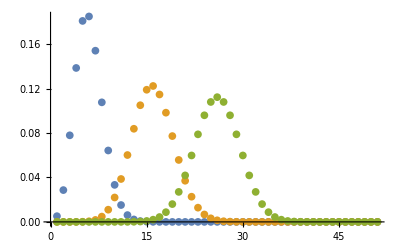

```mathematica
ListPlot[{Table[PDF[BinomialDistribution[50, 0.1],k],{k,0,50}],Table[PDF[BinomialDistribution[50, 0.3],k],{k,0,50}],Table[PDF[BinomialDistribution[50, 0.5],k],{k,0,50}]},PlotRange->All]
```

不連続なので積分できない ->  積分のかわりに足し合わせると:

```mathematica
Table[PDF[BinomialDistribution[50, 0.1], k], {k, 0, 50}]//Tr
```

1.

#### その他の分布 : 負の二項分布

```mathematica
PDF[NegativeBinomialDistribution[n, p], k]
```

Piecewise[{{(1-p)^k p^n Binomial[-1+k+n,-1+n], k≥0}, {0, True}}]

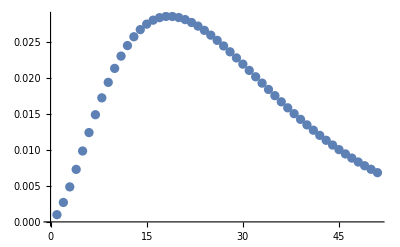

```mathematica
ListPlot[Table[PDF[NegativeBinomialDistribution[3, 0.1],k],{k,0,50}],PlotRange->All]
```

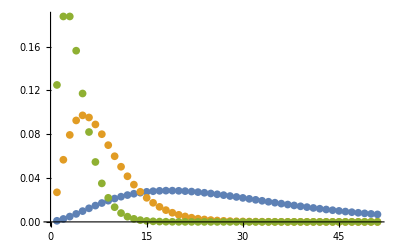

```mathematica
ListPlot[{Table[PDF[NegativeBinomialDistribution[3, 0.1],k],{k,0,50}],Table[PDF[NegativeBinomialDistribution[3, 0.3],k],{k,0,50}],Table[PDF[NegativeBinomialDistribution[3, 0.5],k],{k,0,50}]},PlotRange->All]
```

```mathematica
ListPlot3D[Table[PDF[NegativeBinomialDistribution[s, p], k],{p,0.1,0.5,0.1},{s,{2,3,4,5}},{k,0,50}],PlotRange->All]
```

-Graphics3D-

分布にはすべての事象が含まれない:

```mathematica
Integrate[PDF[NegativeBinomialDistribution[5, 0.5], k], {k, 0, Infinity}]
```

0.988035

#### その他の分布 : poisson分布

```mathematica
PDF[PoissonDistribution[μ], k]
```

Piecewise[{{(ⅇ^-μ μ^k)/(k!), k≥0}, {0, True}}]

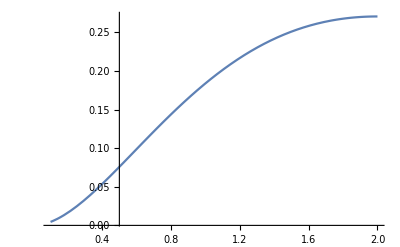

```mathematica
Plot[PDF[PoissonDistribution[n], 2],{n,0.1,2},PlotRange->All]
```

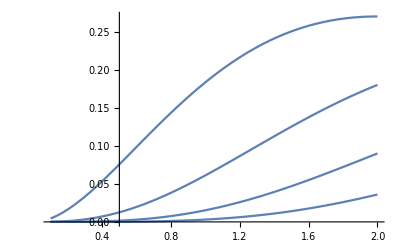

```mathematica
Plot[Table[PDF[PoissonDistribution[n], k],{k,2,5}],{n,0.1,2},PlotRange->All]
```

```mathematica
Integrate[PDF[PoissonDistribution[n], 2],{n,0,Infinity}]
```

1

#### その他の分布 : Zip族

Zipf分布: Zipfの法則 -アイテムの出現回数とそのランクを掛けたものがほぼ一定である- に基づく

```mathematica
??ZipfDistribution
```

ZipfDistribution[ρ] 母数 ρ のゼータ分布を表す．
ZipfDistribution[n,ρ] 範囲 n のZipf分布を表す．

Attributes[ZipfDistribution]={NHoldAll,Protected,ReadProtected}

下記は、データのサイズが4の場合のランクが1から4位までの生産量比

```mathematica
PDF[ZipfDistribution[4, 1], {1, 2, 3, 4}] // N
```

{0.702439,0.17561,0.0780488,0.0439024}

```mathematica
PDF[ZipfDistribution[ρ], k]
```

Piecewise[{{k^(-1-ρ)/Zeta[1+ρ], k≥1}, {0, True}}]

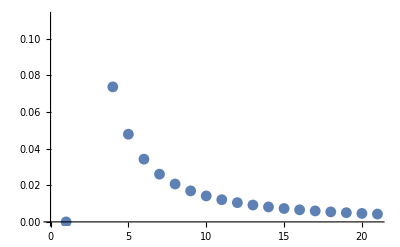

```mathematica
ListPlot[Table[PDF[ZipfDistribution[0.5], k],{k,0,20}]]
```

積分は発散しない :

```mathematica
Integrate[PDF[ZipfDistribution[0.5], k],{k,0,Infinity}]
```

0.765587

20151105

20151112(休講)

zipf関数; r=rank:ランク、f:頻度、a:係数、c:係数。
f × r = c
f × r^a = c ; a = 1
通常、aはきわめて1に近くなるとされる。aを計ることによって、不均衡の度合いを見積もれる。

```mathematica
f=zipf[rank_,a_,c_]:=c*rank^(-a)
```

```mathematica
fitargs=FindFit[Map[#[[2]]&,worldShips],zipf[rank,a,c],{a,c},rank]
```

{a→0.929126,c→5963.12}

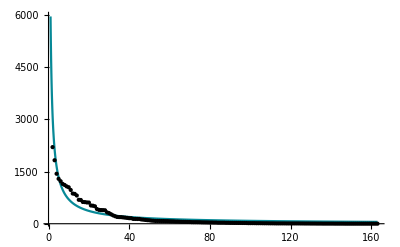

```mathematica
Plot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{#2,#1[[2]]}]]&,worldShips],PlotRange->All]
```

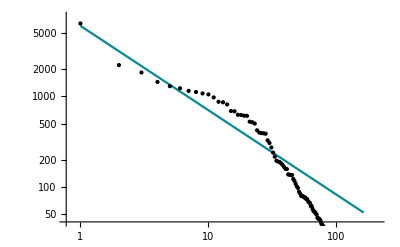

```mathematica
gobjLLP=LogLogPlot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{Log[#2],Log[#1[[2]]]}]]&,worldShips]]
```

ロトカの法則: x:論文の件数、y:それぞれx件の貢献をした著者の割合、n:係数、c:係数のとき、
x^n × y = c

OrlovとChitashviliによれば、Zipf族の関数はつぎの定義のように一般化できる

```mathematica
orlovZ[m]:=Integrate[(Log[1+x]^(γ-1) x^α)/((1+x)^(m+1) (1+x)^β),{x,0,Infinity}]/Integrate[(Log[1+x]^(γ-1) x^(α-1))/((1+x)^(β+1)),{x,0,Infinity}]
```

```mathematica
Timing[orlovZ[m]]
```

{11.4543,(∫_0^∞ x^α (1+x)^(-1-m-β) Log[1+x]^(-1+γ)ⅆx)/(∫_0^∞ x^(-1+α) (1+x)^(-1-β) Log[1+x]^(-1+γ)ⅆx)}

Zipfの法則

```mathematica
Timing[orlovZ[m]/.{α->1,β->1,γ->1}]
```

{14.1139,ConditionalExpression[1/(m+m^2),Re[m]>0]}

Yuleの法則

```mathematica
Timing[orlovZ[m] /. {β -> α, γ -> 1}]
```

{22.4946,ConditionalExpression[(α Gamma[m] Gamma[1+α])/Gamma[1+m+α],Re[α]>0&&Re[m]>0]}

Yule-Simonの法則

```mathematica
Timing[orlovZ[m]/.{α->1,γ->1}]
```

{15.3987,ConditionalExpression[β/((-1+m+β) (m+β)),Re[β]>0&&Re[m+β]>1]}

## 図表表示法

### 補間・スムージング・フィルタリング・フィッテイング

#### 補間

```mathematica
??ListInterpolation
```

ListInterpolation[array] 与えられた値の配列を補間する近似関数を表すInterpolatingFunctionオブジェクトを作成する．
ListInterpolation[array,{{x_min,x_max},{y_min,y_max},…}] array  の各値の座標を決めるグリッド域を指定する．

Attributes[ListInterpolation]={Protected}
 
Options[ListInterpolation]={InterpolationOrder→3,Method→Automatic,PeriodicInterpolation→False}

```mathematica
f=ListInterpolation[{1,4.1,9.2,15,26}]
```

InterpolatingFunction[{{1., 5.}}, <>]

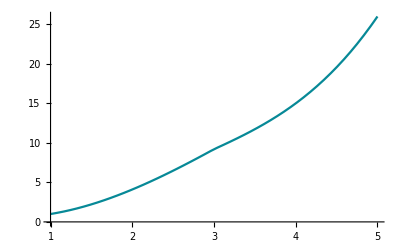

```mathematica
Plot[f[x],{x,1,5}]
```

InterpolatingFunction::dmval: 入力値{0.000122571}は補間関数のデータ範囲外です．外挿が使用されます．

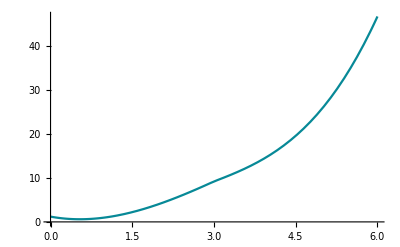

```mathematica
Plot[f[x],{x,0,6}]
```

#### 移動平均

```mathematica
??MovingAverage
```

MovingAverage[list,r] r 個の要素を平均することで計算した list の移動平均を返す．
MovingAverage[list,{w_1,w_2,…,w_r}] 重み w_i で計算した list の移動平均を返す．

Attributes[MovingAverage]={Protected,ReadProtected}

```mathematica
MovingAverage[{a,b,c,d,e},2]
```

{(a+b)/2,(b+c)/2,(c+d)/2,(d+e)/2}

#### 畳み込み

(f * g)(t) = ∫f(x)g(t-x)dx

see also: 内積 : f^Tg = ∫f(x)g(x)dx

```mathematica
??Convolve
```

RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "]"}] 式 StyleBox["f", "TI"]と StyleBox["g", "TI"] の StyleBox["x", "TI"] についてのたたみ込みを返す．
RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 多次元たたみ込みを返す．

Attributes[Convolve]={Protected,ReadProtected}

たたみ込みは一般に関数を滑らかにする：

```mathematica
Remove[f0,f0,t0,t1,t2,t3]
```

Remove::remal: シンボルf0はすでに消去されました．

```mathematica
f0=UnitBox[t0]; (*もとの関数*)
```

```mathematica
f1=Convolve[f0,f0,t0,t1] (*一回畳み込み*)
```

UnitTriangle[t1]

```mathematica
f2=Convolve[f1,f1,t1,t2] (*2回畳み込み*)
```

Piecewise[{{1/6 (4-6 t2^2-3 t2^3), -1<t2<0}, {1/3 (2+3 t2-t2^3), t2==0}, {1/6 (-6 t2-6 t2^2-t2^3), t2==-1}, {1/6 (8-12 t2+6 t2^2-t2^3), 1<t2<2}, {1/6 (6 t2-6 t2^2+t2^3), t2==1}, {1/6 (8+12 t2+6 t2^2+t2^3), -2<t2<-1}, {1/6 (4-6 t2^2+3 t2^3), 0<t2<1}, {0, True}}]

```mathematica
f3=Convolve[f2,f2,t2,t3]; (*3回畳み込み*)
```

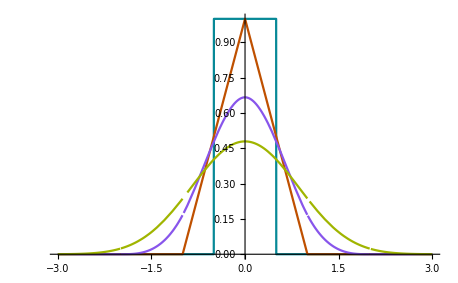

```mathematica
Plot[Evaluate[{f0,f1,f2,f3}/.{t0->x,t1->x,t2->x,t3->x}],{x,-3,3}]
```

```mathematica
Integrate[(f0/.t0->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f1/.t1->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f2/.t2->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f3/.t3->x),{x,-Infinity,Infinity}]
```

1

```mathematica
??ListConvolve
```

RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"]}], "]"}] 核 StyleBox[RowBox[{"ker", " "}], "TI"]と StyleBox["list", "TI"] のたたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["k", "TI"]}], "]"}] StyleBox["ker", "TI"] の StyleBox["k", "TI"] 次の要素がStyleBox["list", "TI"] の各要素と揃えられる循環たたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] 最初の要素が RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", "1", "]"}], "]"}], " ", RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], "]"}], "]"}]}]を含み，最後の要素が RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", RowBox[{"-", "1"}], "]"}], "]"}], " ", RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]], "]"}], "]"}]}]を含む循環たたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["p", "TI"]}], "]"}] StyleBox["list", "TI"] の最後が要素 StyleBox[RowBox[{"p", " "}], "TI"]の反復で充填されるような，たたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["list", "TI"] の最後が SubscriptBox[StyleBox["p", "TI"], StyleBox["i", "TI"]] で循環反復充填されるたたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"]}], "]"}] StyleBox["g", "TI"] がTimesの代りに，StyleBox["h", "TI"] がPlusの代りに使われる一般化されたたたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"], ",", StyleBox["lev", "TI"]}], "]"}] StyleBox["ker", "TI"] と StyleBox["list", "TI"] でレベル StyleBox["lev", "TI"] の要素を使い，たたみ込みを形成する．

Attributes[ListConvolve]={Protected}

```mathematica
ListConvolve[{x,y},{a,b,c,d,e,f}]
```

{b x+a y,c x+b y,d x+c y,e x+d y,f x+e y}

自分自身のリスト畳み込み:

```mathematica
Array[a, 10]
```

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10]}

を、window幅3で畳み込み。

```mathematica
Partition[Array[a,10],3,1]
```

{{a[1],a[2],a[3]},{a[2],a[3],a[4]},{a[3],a[4],a[5]},{a[4],a[5],a[6]},{a[5],a[6],a[7]},{a[6],a[7],a[8]},{a[7],a[8],a[9]},{a[8],a[9],a[10]}}

```mathematica
Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[3],a[2],a[1]},{a[4],a[3],a[2]},{a[5],a[4],a[3]},{a[6],a[5],a[4]},{a[7],a[6],a[5]},{a[8],a[7],a[6]},{a[9],a[8],a[7]},{a[10],a[9],a[8]}}

```mathematica
Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[1] a[3],a[2]^2,a[1] a[3]},{a[2] a[4],a[3]^2,a[2] a[4]},{a[3] a[5],a[4]^2,a[3] a[5]},{a[4] a[6],a[5]^2,a[4] a[6]},{a[5] a[7],a[6]^2,a[5] a[7]},{a[6] a[8],a[7]^2,a[6] a[8]},{a[7] a[9],a[8]^2,a[7] a[9]},{a[8] a[10],a[9]^2,a[8] a[10]}}

```mathematica
Map[Tr[#]&,Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]]
```

{a[2]^2+2 a[1] a[3],a[3]^2+2 a[2] a[4],a[4]^2+2 a[3] a[5],a[5]^2+2 a[4] a[6],a[6]^2+2 a[5] a[7],a[7]^2+2 a[6] a[8],a[8]^2+2 a[7] a[9],a[9]^2+2 a[8] a[10]}

注意: 畳み込みは、一般的に、対象となる関数が返す値の範囲が、0 ≤ f(x) ≤ 1。
さらに、畳み込み前と畳み込み後において、マイナス無限大からプラス無限大の積分が1となるように調整できれば扱いやすい。

※畳み込みは、一種の強度 (Intensity)を取るものであり、フーリエ変換やウエーブレット変換の考えに近い。

#### フーリエ変換/ローパスフィルター(1次元)

フーリエ変換は、時間関数:f(t)を周波数関数:F(w)に変換する。逆フーリエ変換は変換された関数F(w)をもとの関数f(t)に戻す。

```mathematica
Integrate[E^(I w t) f[t],{t,t0,t1}]
```

∫_t0^t1 ⅇ^(ⅈ t w) f[t]ⅆt

サインカーブを生成

```mathematica
li=Table[Sin[x]//N,{x,0,30,0.05}];
```

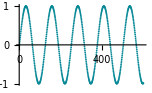

```mathematica
ListPlot[li]
```

フーリエ変換:

```mathematica
fli=Fourier[li];
```

パワースペクトル(周波数区分ごとの強度):

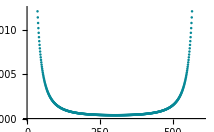

```mathematica
Abs[fli]^2//ListPlot
```

そのまま逆フーリエ変換:

```mathematica
if=InverseFourier[fli];
```

実数部をプロット:

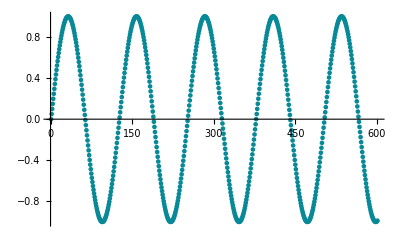

```mathematica
ListPlot[Map[Re,if]]
```

ノイズ付きサインカーブを生成

```mathematica
li=Table[Sin[x]+RandomReal[{-0.3,0.3}]//N,{x,0,30,0.05}];
```

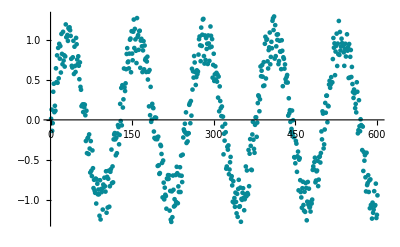

```mathematica
ListPlot[li]
```

フーリエ変換:

```mathematica
fli=Fourier[li];
```

```mathematica
fli//Length
```

601

ローパスフィルターもどきを生成:

```mathematica
flt=({Table[1,{50}],Table[0,{551}]}//Flatten);
```

ローパスフィルタをかけフーリエ逆変換:

```mathematica
iff=InverseFourier[fli flt];
```

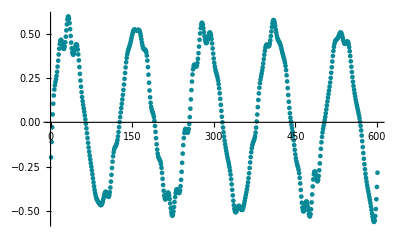

```mathematica
Map[Re,iff]//ListPlot
```

組み込みのローパスフィルター

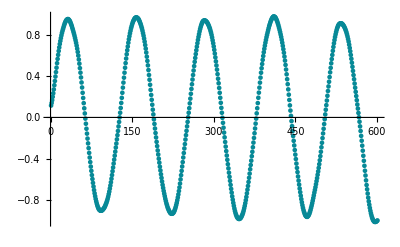

```mathematica
ListPlot[LowpassFilter[li,Pi/32]]
```

#### ガウシアンフィルター(2次元)

重み付き移動平均の一種。ひとつの要素に対して、自身と近傍の重み付き平均をその要素の新しい値とする。

ga() は各重みを計算する。

```mathematica
ga[x_,y_,s_]:=1/(2Pi s^2) E^(-(x^2+y^2)/(2s^2))
```

```mathematica
Plot3D[ga[x,y,2Pi],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
w=Table[ga[x,y,1/Sqrt[2Pi]],{x,-1,1},{y,-1,1}]
```

{{ⅇ^(-2 π),ⅇ^-π,ⅇ^(-2 π)},{ⅇ^-π,1,ⅇ^-π},{ⅇ^(-2 π),ⅇ^-π,ⅇ^(-2 π)}}

```mathematica
totalw=Total[w,Infinity]
```

1+4 ⅇ^(-2 π)+4 ⅇ^-π

```mathematica
w/totalw
```

{{ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)},{ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),1/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)},{ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)}}

gat () は重みのテーブルを作成する。

```mathematica
gat[r_,s_]:=Module[{w,totalw},
w=Table[ga[x,y,s],{x,-r,r},{y,-r,r}];
totalw=Total[w,Infinity];
w/totalw
]
```

```mathematica
gat[1,1/Sqrt[2Pi]]//TableForm
```

ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)
ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | 1/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)
ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)

以下のような行列があったとき、

```mathematica
(t=Table[1,{x,3},{x,3}])//TableForm
```

1 | 1 | 1
1 | 1 | 1
1 | 1 | 1

上の行列の中央の値が以下のように変更される:

```mathematica
Total[t*gat[1,1/Sqrt[2Pi]],Infinity]//N
```

1.

Mathematicaにはより調整されたGaussianFilterが用意されている:

```mathematica
GaussianFilter[t,{1,1/Sqrt[2Pi]}]
```

{{0.127554,1.06846,3.59859},{1.06846,0.273858,1.06846},{3.59859,1.06846,0.127554}}

```mathematica
Array[a, {3, 3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

```mathematica
GaussianFilter[Table[1,{x,3},{x,3}],{1,1}][[2,2]]
```

1.

#### フィッテイング

```mathematica
??Fit
```

Fit[data,funs,vars] 変数 vars の関数 funs の線形な組合せで，与えられたデータの最小二乗法フィットを行う．

Attributes[Fit]={Protected}

```mathematica
l1=Table[n+RandomReal[{-1,1}],{n,20}]
```

{1.77847,2.40703,3.75922,3.76019,5.47608,6.01325,6.21187,7.34968,8.2711,9.14559,10.8581,12.3371,13.2659,14.1694,14.1663,16.3901,17.6836,18.8847,18.5385,20.8971}

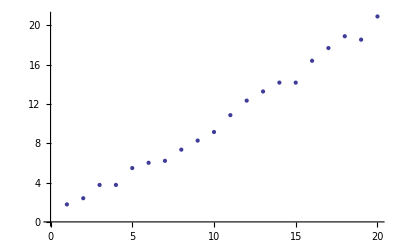

```mathematica
ListPlot[l1]
```

```mathematica
Fit[l1,{x},x]
```

1.00638 x

```mathematica
Fit[l1,{1,x},x]
```

0.004993+1.00602 x

```mathematica
Fit[l1,{1,x,x^2},x]
```

0.933295+0.752843 x+0.0120559 x^2

```mathematica
??FindFit
```

FindFit[data,expr,pars,vars] 変数 vars の関数 expr が data に最もフィットするようなパラメータ pars の数値を求める．
FindFit[data,{expr,cons},pars,vars] パラメータの制約条件 cons のもとで最高のフィットを求める．

Attributes[FindFit]={Protected}
 
Options[FindFit]={AccuracyGoal→Automatic,Compiled→Automatic,EvaluationMonitor→None,Gradient→Automatic,MaxIterations→Automatic,Method→Automatic,NormFunction→Norm,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→Automatic}

```mathematica
pr=Table[Prime[x], {x, 20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
FindFit[pr,a x Log[b+c x],{a,b,c},x]
```

{a→1.42076,b→1.65558,c→0.534645}

#### 最小自乗法の説明

3点、p1、p2、p3を直線y = b + axにフィットさせる。

```mathematica
p1={1,2};p2={2,4};p3={3,5}
```

{3,5}

```mathematica
data={p1,p2,p3}
```

{{1,2},{2,4},{3,5}}

Fit[]関数によるフィット

```mathematica
line=Fit[data,{1,x},x]
```

0.666667+1.5 x

フィットのステップ

フィットさせる関数を設定、求める係数は、a、b

```mathematica
f[x_]:=a+b x
```

説明変数の値を関数に代入

```mathematica
ft=Table[f[data[[n,1]]],{n,3}]
```

{a+b,a+2 b,a+3 b}

目的変数に値を設定

```mathematica
o=Table[data[[n,2]],{n,3}]
```

{2,4,5}

関数の出力と目的変数の値との差の自乗和を計算、この自乗和を最小にすることが目的

```mathematica
ds=Tr[(ft-o)^2]
```

(-2+a+b)^2+(-4+a+2 b)^2+(-5+a+3 b)^2

求めるべき係数のひとつ、aで微分

```mathematica
eq1=D[ds,a]//Expand
```

-22+6 a+12 b

求めるべき係数のもうひとつ、bで微分

```mathematica
eq2=D[Expand[ds],b]
```

-50+12 a+28 b

ふたつの条件を満たすa、bを求める

```mathematica
Solve[{eq1==0,eq2==0},{a,b}]
```

{{a→2/3,b→3/2}}

#### 最尤法の説明

Normal distribution:

```mathematica
nd[z_,m_,s_]:=E^(-(z-m)^2/(2s^2))
```

3点、p1、p2、p3を直線y = b + axにフィットさせる。

```mathematica
p1={1,2};p2={2,4};p3={3,5}
```

{3,5}

```mathematica
data={p1,p2,p3}
```

{{1,2},{2,4},{3,5}}

フィットさせる関数を設定、求める係数は、a、b

```mathematica
f[x_]:=a+b x
```

説明変数の値を関数に代入

```mathematica
ft=Table[f[data[[n,1]]],{n,3}]
```

{a+b,a+2 b,a+3 b}

説明変数の値に対応する確率を式で与える

```mathematica
nt=Table[nd[z[n],ft[[n]],s],{n,3}]
```

{ⅇ^(-(-a-b+z[1])^2/(2 s^2)),ⅇ^(-(-a-2 b+z[2])^2/(2 s^2)),ⅇ^(-(-a-3 b+z[3])^2/(2 s^2))}

目的変数に値を設定

```mathematica
o=Table[data[[n,2]],{n,3}]
```

{2,4,5}

目的変数の値を対応する確率密度関数に代入

```mathematica
pre=nt/.Table[z[n]->o[[n]],{n,3}]
```

{ⅇ^(-(2-a-b)^2/(2 s^2)),ⅇ^(-(4-a-2 b)^2/(2 s^2)),ⅇ^(-(5-a-3 b)^2/(2 s^2))}

確率密度関数の掛け合わせの値が最大になるよう係数を求める

=> log(確率密度関数)の足し合わせが最大になるよう係数を求める

```mathematica
Log[E,pre]
```

{Log[ⅇ^(-(2-a-b)^2/(2 s^2))],Log[ⅇ^(-(4-a-2 b)^2/(2 s^2))],Log[ⅇ^(-(5-a-3 b)^2/(2 s^2))]}

```mathematica
el=Simplify[Log[E,pre],{Element[a,Reals],Element[b,Reals],Element[s,Reals],s>0}]
```

{-(-2+a+b)^2/(2 s^2),-(-4+a+2 b)^2/(2 s^2),-(-5+a+3 b)^2/(2 s^2)}

```mathematica
e0=(Tr[el])
```

-(-2+a+b)^2/(2 s^2)-(-4+a+2 b)^2/(2 s^2)-(-5+a+3 b)^2/(2 s^2)

求めるべき係数のひとつ、aで微分

```mathematica
eq1=D[e0,a]
```

-(-2+a+b)/s^2-(-4+a+2 b)/s^2-(-5+a+3 b)/s^2

求めるべき係数のもうひとつ、bで微分

```mathematica
eq2=D[e0,b]
```

-(-2+a+b)/s^2-(2 (-4+a+2 b))/s^2-(3 (-5+a+3 b))/s^2

ふたつの条件を満たすa、bを求める

```mathematica
Solve[{eq1==0,eq2==0},{a,b}]
```

{{a→2/3,b→3/2}}